```mathematica
{m1, m2, θb0, θs0, n, l,λ,g} = {30, 1, 3π/4, π/2, 1, 10,1/10,9.8}
```

{30,1,(3 π)/4,π/2,1,10,1/10,9.8}

```mathematica
lengths = RandomVariate[UniformDistribution[{0,l}],3]
```

{1.33831,0.0444567,3.21266}

```mathematica
f[a_,b_,c_] = c*Cos[a]+b^2*Sin[a];
```

```mathematica
l1=lengths[[1]];
l2=lengths[[1]]+lengths[[2]];
(*l2=3*l1;*)
ls=lengths[[3]];
mb = λ*Sqrt[m1]*(l1+l2);
Ib=0.25*mb*(l1+l2)^2;
lb=(l2-l1)/2;
αb = m2*l2*ls/(m1*l1*l1+m2*l2*l2+mb*lb*lb+Ib);
αs = l2/ls;
ωb = (m1*l1-m2*l2-mb*lb)*g/(m1*l1*l1+m2*l2*l2+mb*lb*lb+Ib);
ωs = g/ls;
s = NDSolve[{θb''[t] ==αb*f[θb[t]-θs[t], θs'[t], θs''[t]] - ωb*Sin[θb[t]],θs''[t] ==αs*f[θs[t]-θb[t], θb'[t], θb''[t]] - ωs*Sin[θs[t]],
θb'[0] == θs'[0] ==0, 
 θb[0] == θb0, θs[0] == θs0},{θb,θs},{t,0,20}];
```

ReplaceAll::reps: {«1»==-0.397679 Sin[InterpolatingFunction[{{«2»}},{5,7,2,{«1»},{«1»},0,0,0,0,Automatic,{},{},False},{{«677»}},{Developer`PackedArrayForm,{«678»},{«2031»}},{Automatic}][t]]+0.00815295 (-Sin[Plus[«2»]] (InterpolatingFunction[«5»][«1»])^2+Cos[Plus[«2»]] InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][t]),InterpolatingFunction[«1»][t]==-«18» Sin[«1»]+«1»,«5»,True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {«1»==-0.397679 Sin[InterpolatingFunction[{{«2»}},{5,7,2,{«1»},{«1»},0,0,0,0,Automatic,{},{},False},{{«677»}},{Developer`PackedArrayForm,{«678»},{«2031»}},{Automatic}][t]]+0.00815295 (-Sin[Plus[«2»]] (InterpolatingFunction[«5»][«1»])^2+Cos[Plus[«2»]] InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][t]),InterpolatingFunction[«1»][t]==-«18» Sin[«1»]+«1»,«5»,True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

ReplaceAll::reps: {«1»==-0.397679 Sin[InterpolatingFunction[{{«2»}},{5,7,2,{«1»},{«1»},0,0,0,0,Automatic,{},{},False},{{«677»}},{Developer`PackedArrayForm,{«678»},{«2031»}},{Automatic}][t]]+0.00815295 (-1. Sin[Plus[«2»]] (InterpolatingFunction[«5»][«1»])^2+Cos[Plus[«2»]] InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][t]),«1»==-8.13577 Sin[«21»[«1»][t]]+«1»,«5»,True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::litarg: To avoid possible ambiguity, the arguments of the dependent variable in «1» should literally match the independent variables.

```mathematica
θb = θb /. First[s];
θs = θs /. First[s];
```

ReplaceAll::reps: {(«1»)''[t]==-6.49934 Sin[(InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}]/.{Equal[«2»],Equal[«2»],False,True,True})[t]]+0.0760627 (-Sin[Plus[«2»]] ((«1»)^(«1»)[«1»])^2+Cos[Plus[«2»]] ReplaceAll[«2»]''[t]),«3»,(InterpolatingFunction[{{0.,20.}},«3»,{Automatic}]/.{InterpolatingFunction[{{«2»}},«3»,{Automatic}][t]==-0.397679 Sin[«1»]+«21» «1»,«4»})[0]==«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
x[t_] = -l2*θb'[t]*Cos[θb[t]] + ls*θs'[t]*Cos[θs[t]];
y[t_] = -l2*θb'[t]*Sin[θb[t]] + ls*θs'[t]*Sin[θs[t]];
```

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

ReplaceAll::reps: {False,False,False,True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {False,False,False,True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

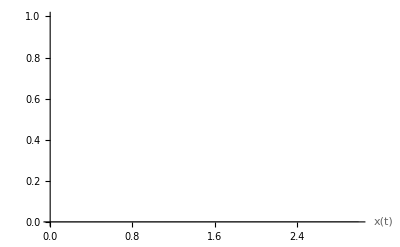

```mathematica
Plot[{x[t],y[t]},{t,0,3},PlotLabels->"Expressions"]
```